# 1D FEA Build

We want to solve the one dimensional damped wave equation
	u_tt+c u_t=k u_xx
on the domain 0<=x<=1 with Dirichlet conditions u(0)=u(1)=0.

Our spatial Weak Form is for all v∈H_0^1((0,1))

∫_0^1 u_tt v dx +c∫_0^1 u_t v dx =-k∫_0^1 u_x v_x dx

We decided to split the domain up at the points  
	p_i=i/(n+1)  for i=1,…,n.

Note there are n internal nodes we are going to need to solve at for n the time dependent nodal values of our solution u_i(t)

We do not need to solve for u_0 or u_(n+1) since the boundary conditions tell us u_0=u_(n+1)=0.

We are going to use our FEA structure and manually build up the matrices for our FEA stuff.

Note: There are n internal nodes v_i for i=1:n

Note: There are n+1 line segments S_i=(v_i,v_(i+1)) for  i=0:n

Note: With this “obvious” counting scheme x_i is right between S_(i-1) and S_i.

The mesh is everything: the nodes; the line segments; the numbering scheme; and the connectivity information.

As before could people remind me to take pics of the board as we go.

## Mesh Pic

Computer will draw things in 2D and 3D.  I need to trick the computer into plotting 1D things!

```mathematica
p[n_,i_]:=i/(n+1.0)
S[n_,i_]:=Interval[{x[n,i],x[n,i+1]}]
```

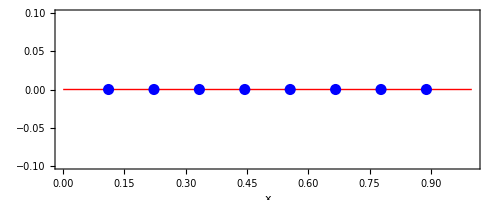

```mathematica
n=8;
Graphics[{
{Red, Line[{{0,0},{1,0}}]},
{Blue, PointSize[0.02],Table[Point[{p[n,i],0}],{i,1,n}]}
},
PlotRange->{Automatic,{-0.1,0.1}},
FrameLabel->{"x"," "},
Frame->True
]
```

From now on we are going to use the vertical direction for the values of “u”.

## Tent Functions

We chose to solve for u as a piecewise linear function of x that satisfies u(0,t)=u(1,t)=0 at all times t and is linear on each interval S_i.  The fancy way to say this is that it has knots (corners) at each x_i.  We organize this by using easily the interpretable piecewise linear tent functions ϕ_i defined below.

```mathematica
ϕ[n_,i_][x_]:=Which[
p[n,i-1]<x<p[n,i],1-(x-p[n,i])/(p[n,i-1]-p[n,i]),
p[n,i]<x<p[n,i+1], 1+(x-p[n,i])/(p[n,i]-p[n,i+1]),
True, 0]
```

Just checking they look correct.

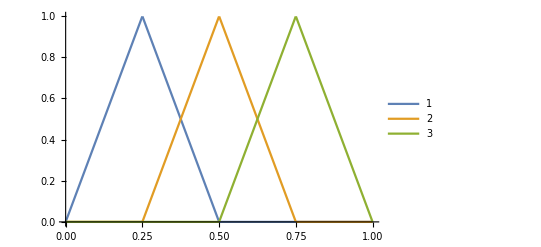

```mathematica
n=3;
Plot[Evaluate[Table[ϕ[n,i][x],{i,1,n}]],{x,0,1},
PlotLegends->Range[1,n]]
```

We are approximately solving inside the class of function that look like
	∑_(i=1)^n a_i(t)ϕ_i(x)
With this choice of nodal “shape function” each a_i is easily interpreted.

a_i(t) is the value of our approximate solution at point p_i and time t!

Since a_0=0 and a_(n+1)=0 because u(0,t)=u(1,t)=0 we do not include them in the sum!

```mathematica
MInvK
```

{{61.6203,-43.6812,11.7043,-3.13617,0.840333,-0.225167,0.0603332,-0.0161662,0.00433161,-0.00116025,0.000309401,-0.0000773502},{-43.6812,73.3246,-46.8173,12.5447,-3.36133,0.900666,-0.241333,0.0646648,-0.0173265,0.00464101,-0.0012376,0.000309401},{11.7043,-46.8173,74.165,-47.0425,12.605,-3.3775,0.904998,-0.242493,0.0649742,-0.0174038,0.00464101,-0.00116025},{-3.13617,12.5447,-47.0425,74.2253,-47.0587,12.6093,-3.37866,0.905307,-0.24257,0.0649742,-0.0173265,0.00433161},{0.840333,-3.36133,12.605,-47.0587,74.2296,-47.0598,12.6096,-3.37874,0.905307,-0.242493,0.0646648,-0.0161662},{-0.225167,0.900666,-3.3775,12.6093,-47.0598,74.2299,-47.0599,12.6096,-3.37866,0.904998,-0.241333,0.0603332},{0.0603332,-0.241333,0.904998,-3.37866,12.6096,-47.0599,74.2299,-47.0598,12.6093,-3.3775,0.900666,-0.225167},{-0.0161662,0.0646648,-0.242493,0.905307,-3.37874,12.6096,-47.0598,74.2296,-47.0587,12.605,-3.36133,0.840333},{0.00433161,-0.0173265,0.0649742,-0.24257,0.905307,-3.37866,12.6093,-47.0587,74.2253,-47.0425,12.5447,-3.13617},{-0.00116025,0.00464101,-0.0174038,0.0649742,-0.242493,0.904998,-3.3775,12.605,-47.0425,74.165,-46.8173,11.7043},{0.000309401,-0.0012376,0.00464101,-0.0173265,0.0646648,-0.241333,0.900666,-3.36133,12.5447,-46.8173,73.3246,-43.6812},{-0.0000773502,0.000309401,-0.00116025,0.00433161,-0.0161662,0.0603332,-0.225167,0.840333,-3.13617,11.7043,-43.6812,61.6203}}

## Weak Form

Substituting u→∑_(i=1)^n a_i(t)ϕ_i(x) into or weak form 
	∫_0^1 u_tt v dx +c∫_0^1 u_t v dx =-k∫_0^1 u_x v_x dx  
gives 
	∑_(i=1)^n a_i''∫_0^1 ϕ_i(x)v dx +c ∑_(i=1)^n a_i'∫_0^1 ϕ_i(x)v dx  =-k∑_(i=1)^n a_i∫_0^1 ϕ_i'(x)v'(x) dx  
Since this must hold for all v∈H_0^1((0,1)) it is actually an infinite number of equations!

An infinite number of equations is a problem!

From Linear Algebra we know we would like the same number of equations as unknowns!

Note: ϕ_j∈H_0^1((0,1)) for j=1:n.

It is VERY convenient that there are n of them.

The simplest thing to do is to take the test functions v to match the trial functions u.

## Matrices

Choosing v=ϕ_j in our weak form gives
	∑_(i=1)^n a_i''∫_0^1 ϕ_i(x)ϕ_j dx +c ∑_(i=1)^n a_i'∫_0^1 ϕ_i(x)ϕ_j dx  =-k∑_(i=1)^n a_i∫_0^1 ϕ_i'(x)ϕ_j'(x) dx

Since j=1:n there are n equations.

Linear equations including ODEs are naturally written using matrices

Define the mass matrix:  M_(j,i)=∫_0^1 ϕ_i(x)ϕ_j (x)dx

Define the stiffness matrix:  K_(j,i)=k∫_0^1 ϕ_i'(x)ϕ_j '(x)dx

Our semi-discretized equation becomes
	∑_(i=1)^n a_i'' M_(j,i) +c ∑_(i=1)^n a_i' M_(j,i)  =-∑_(i=1)^n a_i K_(j,i)   
or 	∑_(i=1)^n M_(j,i)a_i'' +c ∑_(i=1)^n M_(j,i)a_i'  =-∑_(i=1)^n K_(j,i)a_i   
or 	M.a''[t]+c M.a'[t]=- K.a[t]

The matrices are easy to compute inefficiently!

```mathematica
KBuild[k_,n_]:= Table[
k*NIntegrate[ϕ[n,j]'[x]*ϕ[n,i]'[x],{x,0,1}],
{j,n},{i,n}]
MBuild[n_]:= Table[
NIntegrate[ϕ[n,j][x]*ϕ[n,i][x],{x,0,1}],
{j,n},{i,n}]
```

```mathematica
n=12; k=0.1;
K=KBuild[k,n];
M=MBuild[n];
MatrixForm[K]
```

(2.6 | -1.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-1.3 | 2.6 | -1.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.3 | 2.6 | -1.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -1.3 | 2.6 | -1.3 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -1.3 | 2.6 | -1.3 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -1.3 | 2.6 | -1.3 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.3 | 2.6 | -1.3 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1.3 | 2.6 | -1.3 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.3 | 2.6 | -1.3 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.3 | 2.6 | -1.3 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.3 | 2.6 | -1.3
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.3 | 2.6)

## Solving the ODEs.

The ODE system
	M.a''[t]+c M.a'[t]=- K.a[t]
is also easy to solve inefficiently!

NDSolveValue::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

InterpolatingFunction[…]

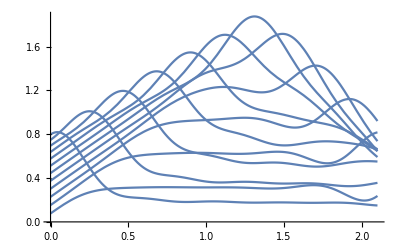

```mathematica
n=12;
K=KBuild[0.1,n];
M=MBuild[n];
c=0.01; TMax=2.1;
a0=Table[ Sin[p[n,i]],{i,1,n}];
ad0=0*a0;
aSol = NDSolveValue[{
M.a''[t]+c M.a'[t]==-K.a[t],
a'[0]==ad0;
a[0]==a0},
a,{t,0, TMax}]
Plot[aSol[t],{t,0, TMax}]
```

InterpolatingFunction[…]

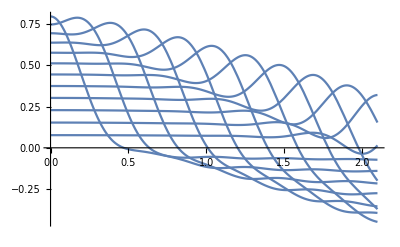

```mathematica
MInvK=Inverse[M].K;
aSol = NDSolveValue[{
a''[t]+c a'[t]==-MInvK.a[t],
a'[0]==ad0,
a[0]==a0},
a,{t,0, TMax}]
Plot[aSol[t],{t,0, TMax}]
```

This is probably not the best way to look at the solution!